# Conformal Barycenter Sampling Examples

This notebook demonstrates the use of the conformal barycenter sampler by computing some example histograms for functions where we know the expected answers and comparing the results.

```mathematica
Exit
```

## Loading the sampler

The first step in using the barycenter sampling package is loading the sampler. From this example file, it’s one directory up:

```mathematica
Get[
Echo@FileNameJoin[{ParentDirectory[NotebookDirectory[]],"CycleSamplerLink.m"}]
]
```

/Users/Henrik/github/CycleSamplerLink/CycleSamplerLink.m

but you should alter the path accordingly if you’re working elsewhere.

The first function in the library is CycleSampleCompressed:

The edgelength vector r must have the property that no single edge has more than half the total length of the polygon.

```mathematica
result=CycleSample["Gyradius",3,{5,1,1,1},10]
```

CycleSamplerLink::badedgelengths: One edge has more than half the total length of the polygon. No closed polygons with these edgelengths exist.

$Failed

Some further failure modes.

```mathematica
result=CycleSample["Gyradius",3,{1,1,1,1},10,"SphereRadii"->anything]
```

CycleSamplerLink::badsphereradii2: The value for the option "SphereRadii" has to be a numerical vector or a String.

$Failed

```mathematica
result=CycleSample["Gyradius",3,{1,1,1,1},10,"SphereRadii"->{1,1}]
```

CycleSamplerLink::badsphereradii: The Length of the vector given as value for option "SphereRadii" does not coincide with the Length of the second argument.

$Failed

```mathematica
result=CycleSample["Some random text",3,{1,1,1,1},10]
```

ERROR: cSampleRandomVariable: Random variable with tag "Some random text" not found. Aborting.

$Failed

Sampling 1 million 4-gons in 3 dimensional space is very fast:

```mathematica
First@AbsoluteTiming[
result=CycleSample["Gyradius",3,{1,1,1,1},1000000];
]
```

Compiling cSampleRandomVariable[3]...

Compilation done. Time elapsed = 1.12872 s.

1.49764

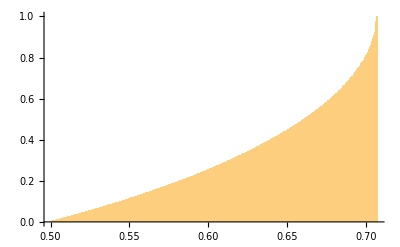

```mathematica
Histogram[result,"Wand","CDF"]
```

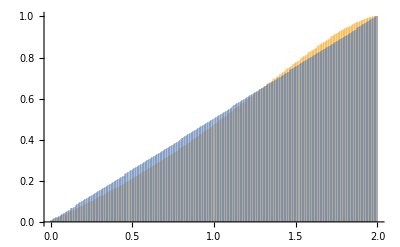

```mathematica
result1=CycleSampleChordLength[3,{1,1,1,1},{1,3},1000000,"QuotientSpace"->False];
result2=CycleSampleChordLength[3,{1,1,1,1},{1,3},1000000,"QuotientSpace"->True];

Histogram[{result1,result2},"Wand","CDF"]
```

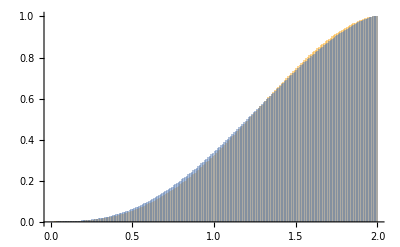

```mathematica
result1=CycleSampleChordLength[4,{1,1,1,1,1,1},{1,3},1000000,"QuotientSpace"->False];
result2=CycleSampleChordLength[4,{1,1,1,1,1,1},{1,3},1000000,"QuotientSpace"->True];

Histogram[{result1,result2},"Wand","CDF"]
```

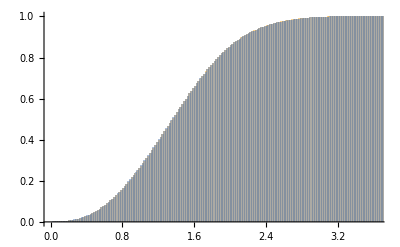

```mathematica
result1=CycleSampleChordLength[3,{1,1,1,1,1,1,1,1},{1,5},1000000,"QuotientSpace"->False];
result2=CycleSampleChordLength[3,{1,1,1,1,1,1,1,1},{1,5},1000000,"QuotientSpace"->True];

Histogram[{result1,result2},"Wand","CDF"]
```

FYI: This lists the paths pf the dynamic libraries generated:

```mathematica
FileNames[
"*"<>CCompilerDriver`CCompilerDriverBase`$PlatformDLLExtension,FileNameJoin[{ParentDirectory[NotebookDirectory[]],"LibraryResources",$SystemID}]
]
```

{}

This deletes the libraries and restarts the package:

```mathematica
CycleSamplerLink`Private`clearLibraries[]
```

```mathematica
FileNames[
"*"<>CCompilerDriver`CCompilerDriverBase`$PlatformDLLExtension,FileNameJoin[{ParentDirectory[NotebookDirectory[]],"LibraryResources",$SystemID}]
]
```

{}